```mathematica
Move[x_,n_,m_]:=Delete[Insert[x,x[[n]],m],n]
```

```mathematica
goCells=;
```

```mathematica
GOTermsDic=Dispatch[Union[#[[1]]->#[[2,3,1,1]]&/@Flatten[Normal[Normal[goCells][[;;,2]]]]]];
```

```mathematica
TermsGoDic=Dispatch[Reverse/@Normal@GOTermsDic];
```

```mathematica
MGo=;
```

```mathematica
FGo=;
```

```mathematica
Partition[
DeleteCases[DeleteCases[Normal[Normal[goCells][[;;,2]]],HoldPattern[_->{__,{{_,"molecular_function"|"cellular_component"(*|"biological_process"*)},_}}],∞]/.HoldPattern[x_->{{y_,__},__}]:>{x,-Log10@y},{_,_?(#<0&)},{2}],
4]
```

```mathematica
GPTerms=(ReverseSortBy[({#[[1,1,1]],SortBy[#,Last][[;;,1,2]]}&/@GatherBy[Join@@MapIndexed[Thread[{#,#2[[1]]}]&,Join@@{#[[1]],Thread[{DeleteCases[#[[2]],Alternatives@@#[[1,;;,1]]],0}]}&/@Thread[{#,Union@@#[[;;,;;,1]]},List,{1}]],#[[1,1]]&]),#[[2]]&]&/@(Partition[
DeleteCases[DeleteCases[Normal[Normal[goCells][[;;,2]]],HoldPattern[_->{__,{{_,"molecular_function"|"cellular_component"(*|"biological_process"*)},_}}],∞]/.HoldPattern[x_->{{y_,__},__}]:>{x,-Log10@y},{_,_?(#<0&)},{2}],
4]));
```

```mathematica
MShoval=;
FShoval=;
```

```mathematica
GPTerms1=Cases[#[[1]]/.GOTermsDic,{Alternatives@@#[[2]],_}]&/@({GPTerms,{MShoval,FShoval}}ᵀ);
```

```mathematica
delimetersM=Length@Split[Reverse@#][[1]]&/@(GPTerms1[[1,;;,2]]ᵀ[[;;3]]);
delimetersF=Length@Split[Reverse@#][[1]]&/@(GPTerms1[[2,;;,2]]ᵀ[[;;3]]);
```

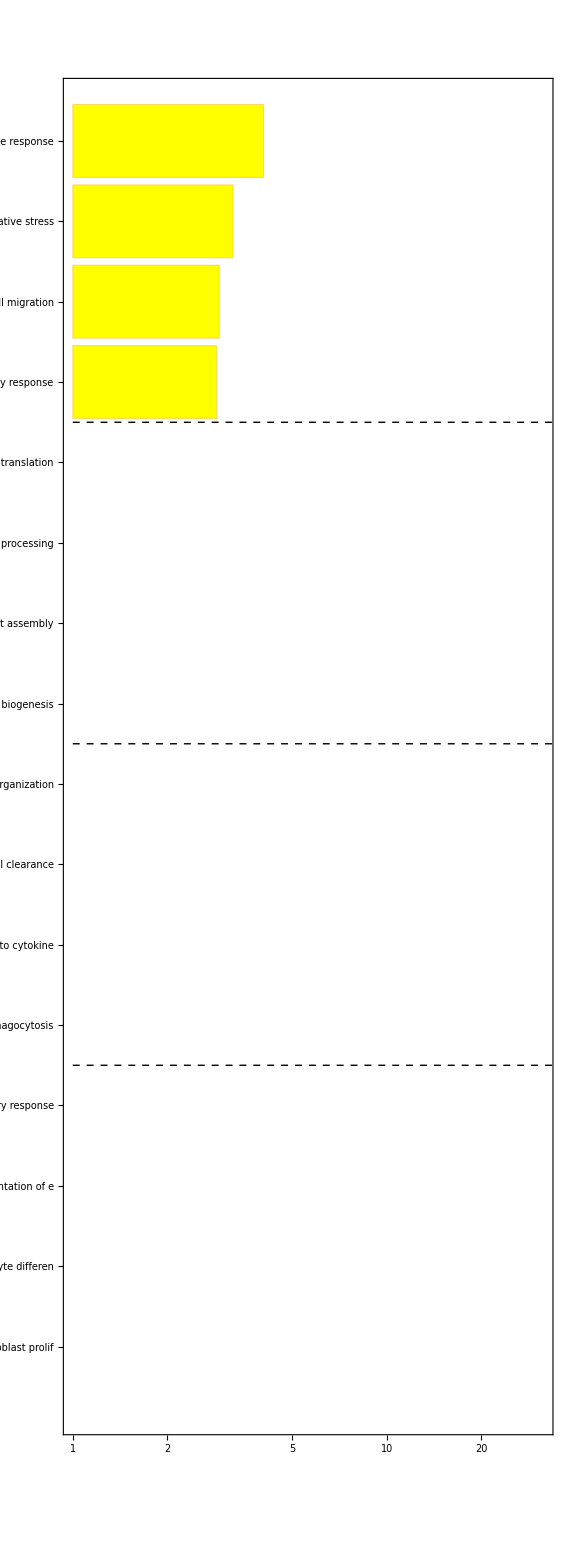
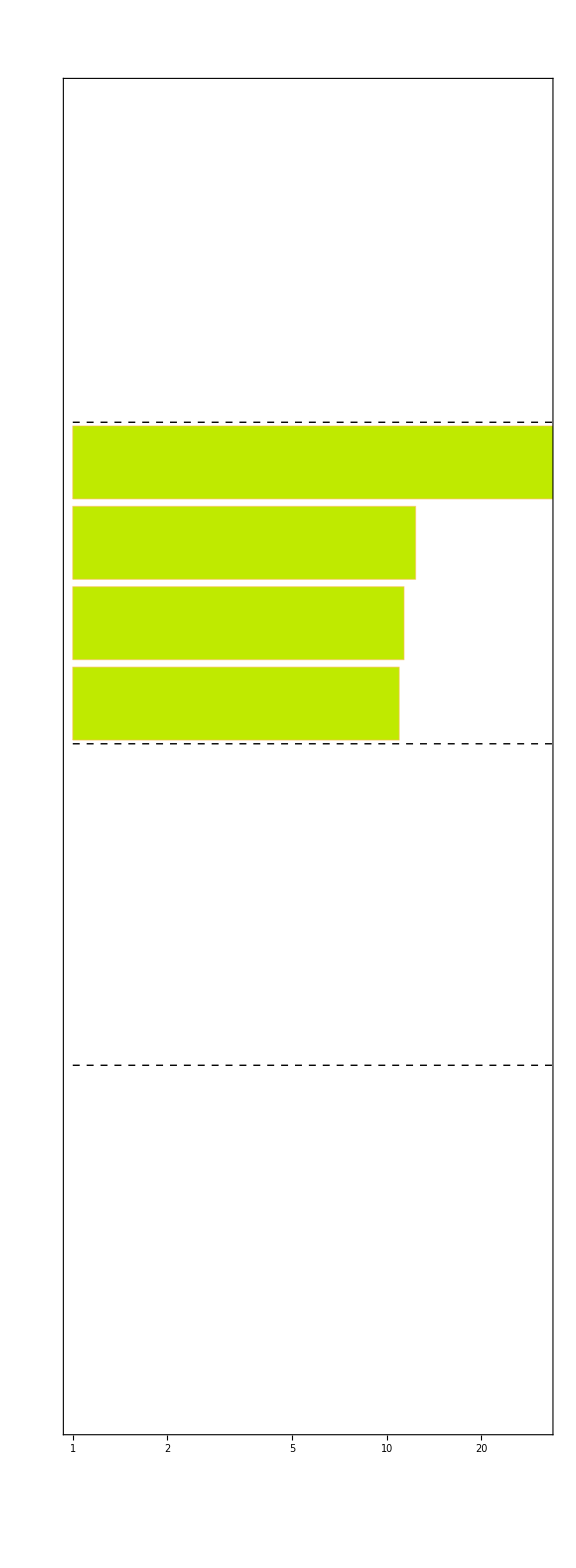
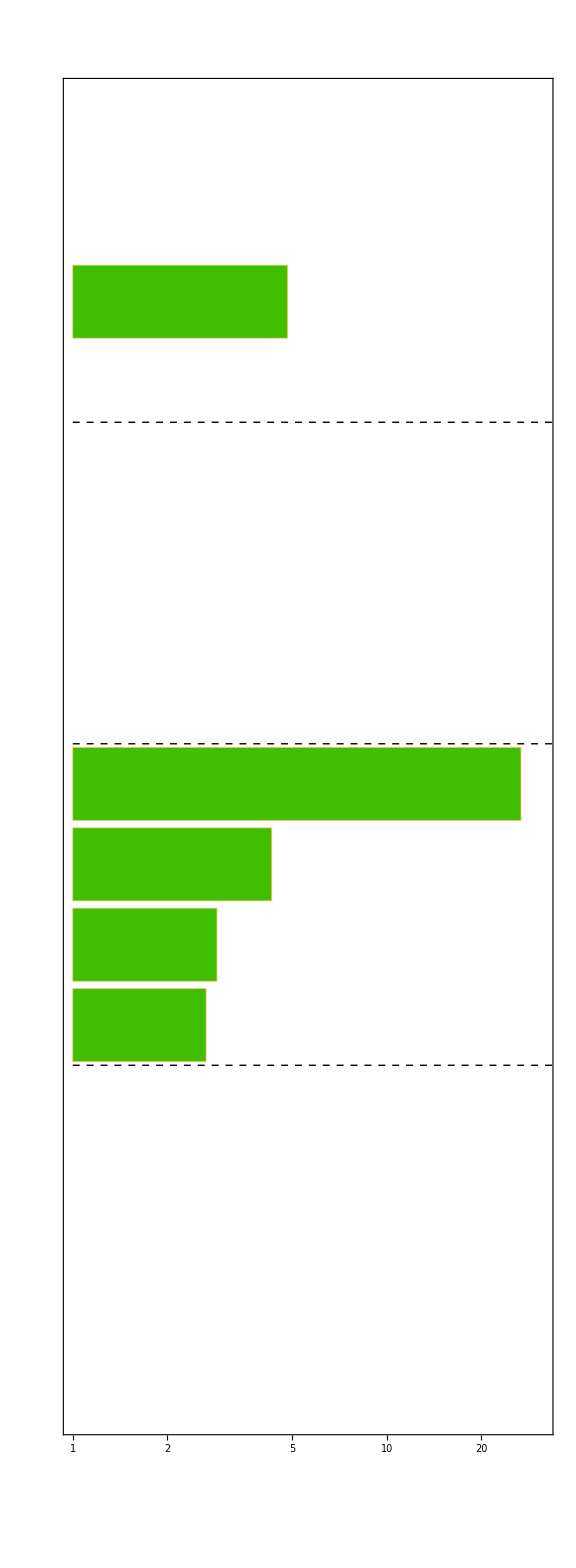
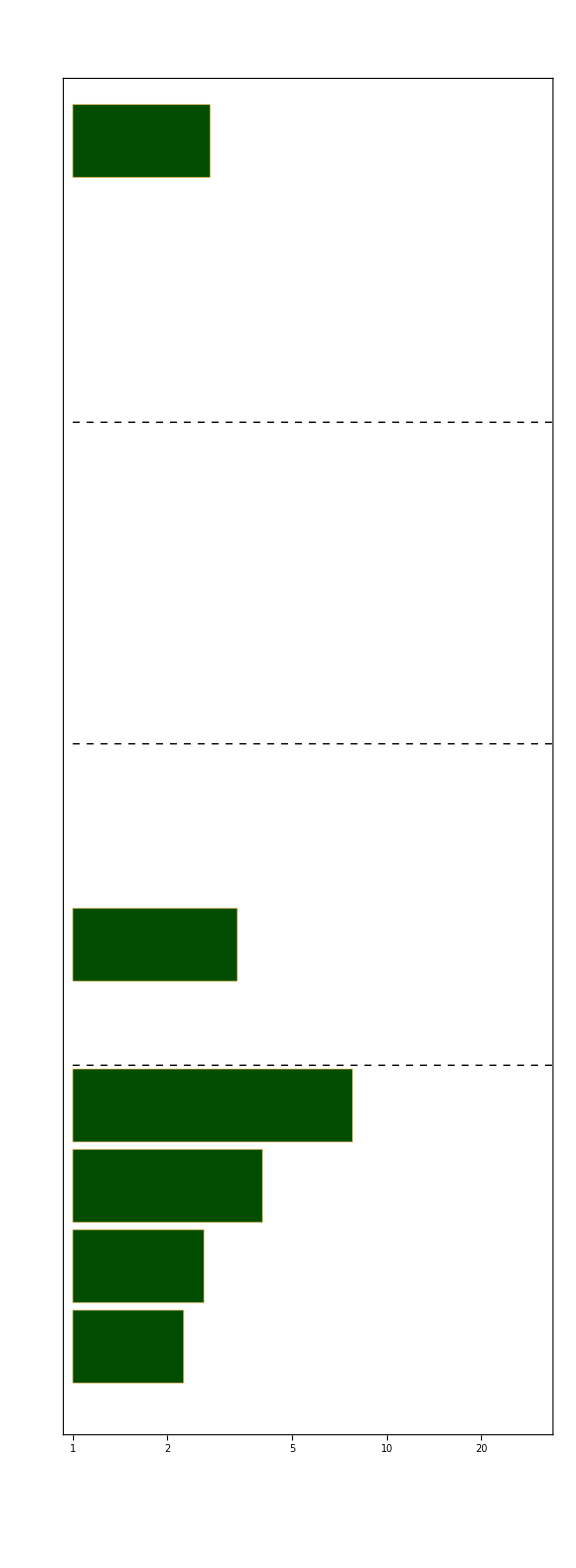
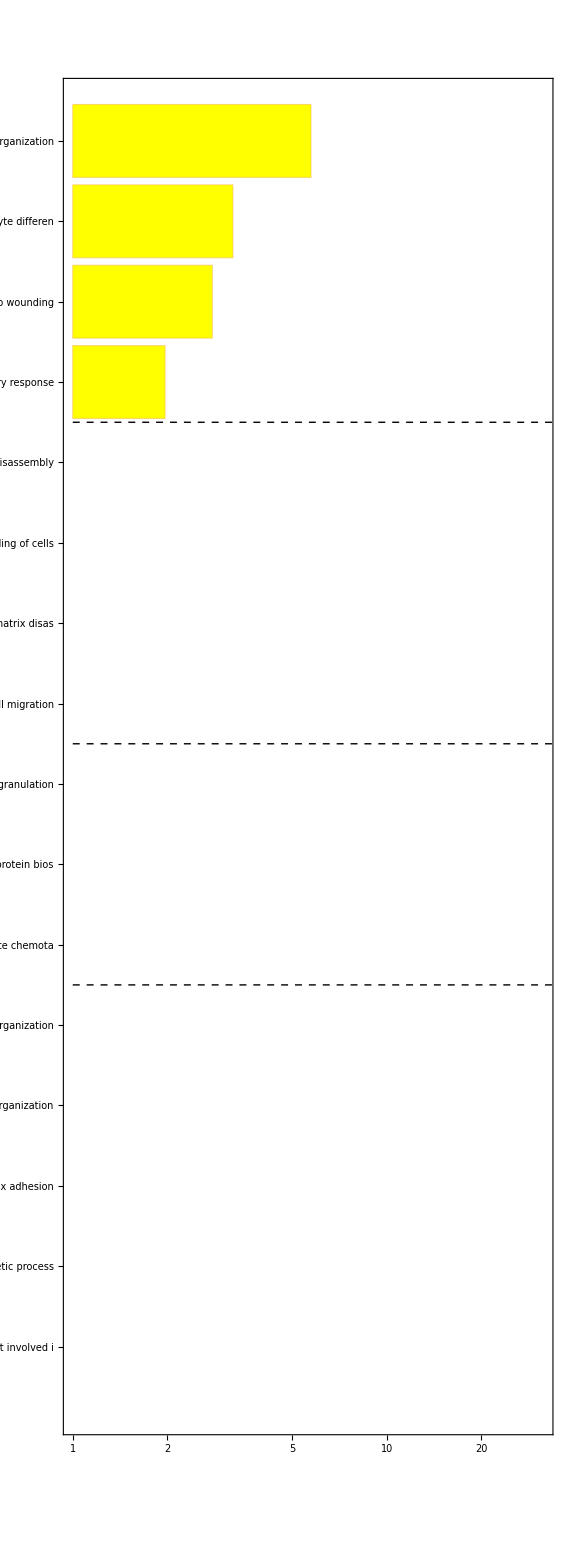
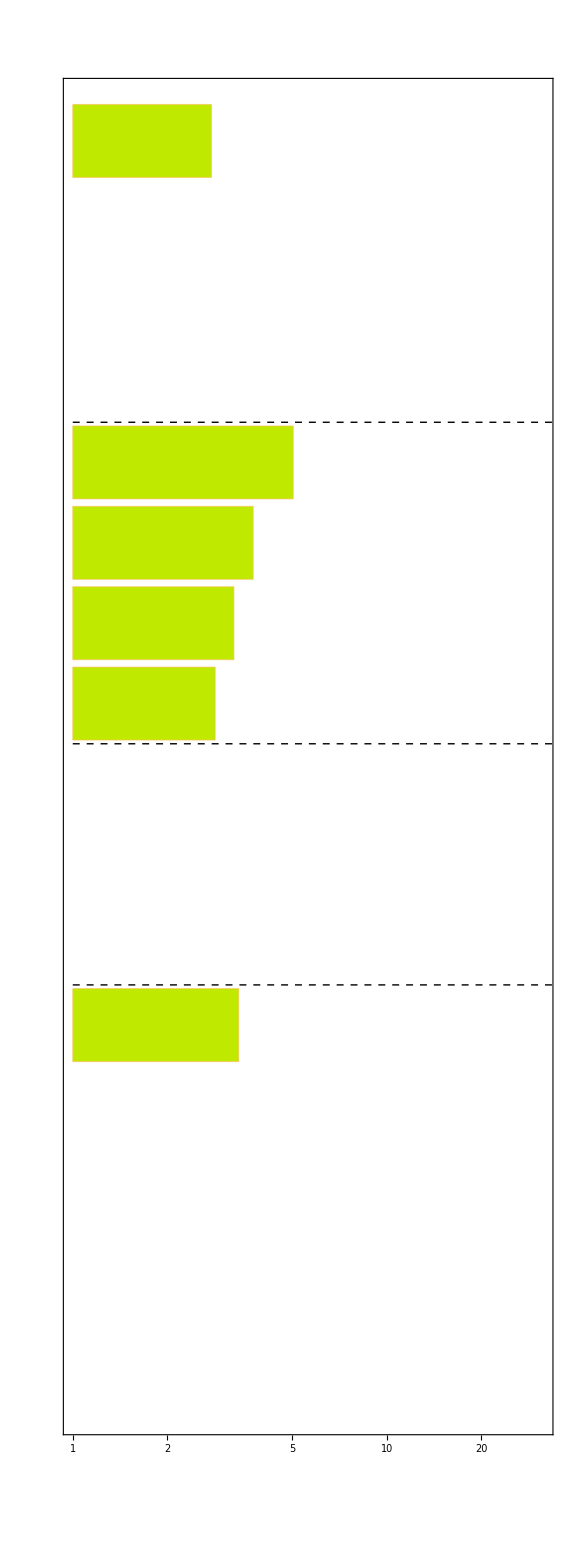
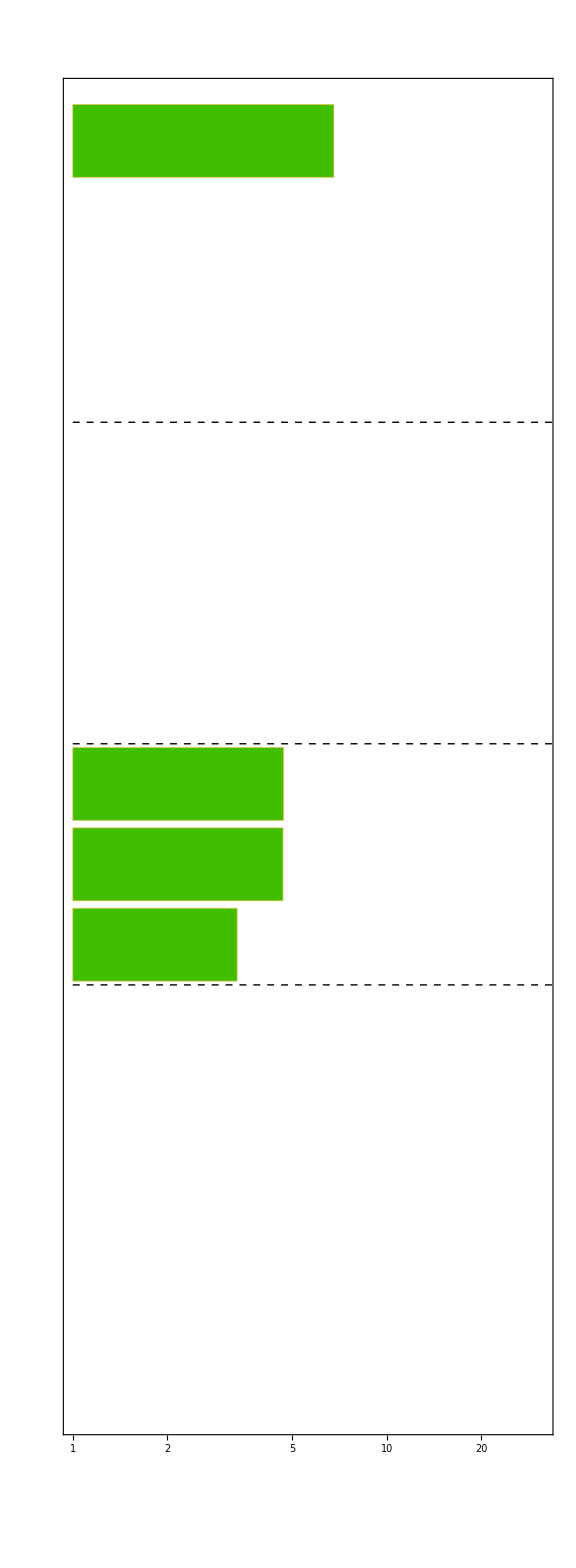
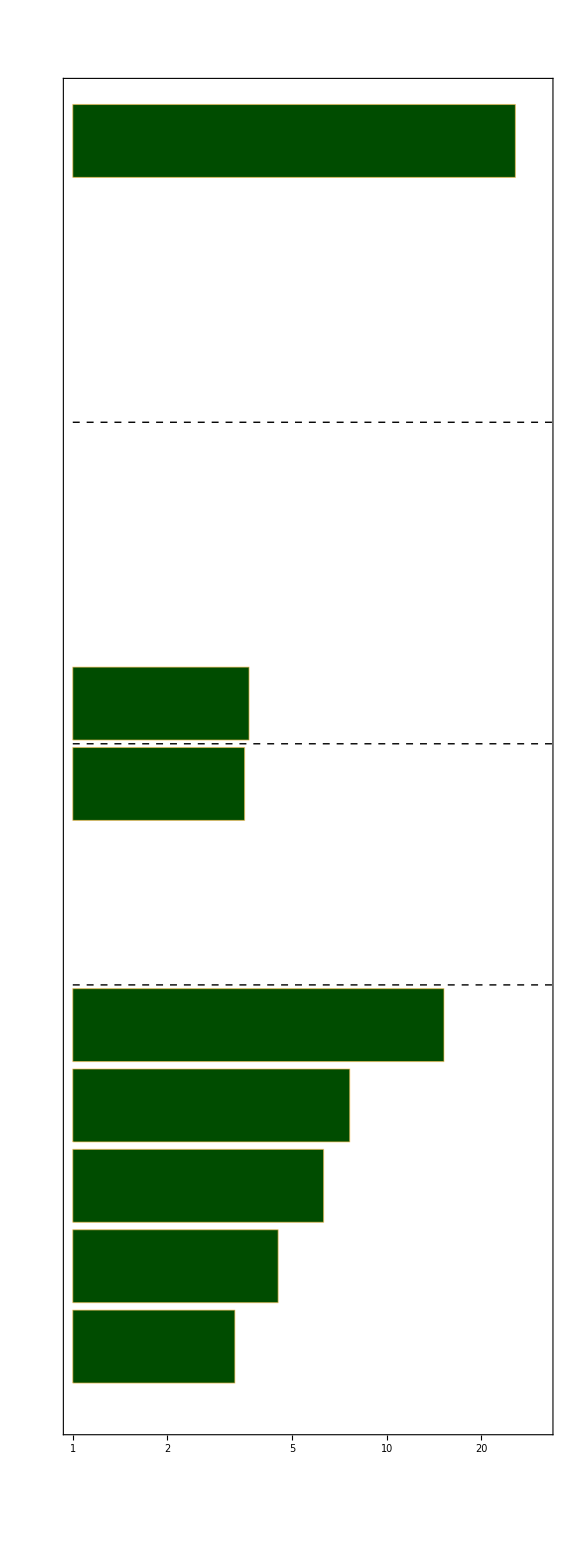

```mathematica
Row[
{Row[
MapIndexed[
BarChart[
Log10@Reverse@#,BarOrigin->Left,AspectRatio->8,Frame->True,ImageSize->Large,PlotRangePadding->None,FrameTicks->{{If[#2[[1]]==1,{Range@Length@#,Reverse@#}ᵀ&@GPTerms1[[1,;;,1]],None],None},{{Log10@#,#}&/@{1,2,5,10,20}(*Automatic*),None}},ChartStyle->{ RGBColor[1, 1, 0],RGBColor[0.75, 0.9166666666666666, 0.],RGBColor[0.25, 0.75, 0.],RGBColor[0, Rational[8, 27], 0]}[[#2[[1]]]],
Epilog->{Dashed,Thin,Line[{{0,#},{100,#}}]&/@({12,8,4}+.5)},PlotRange->{{0,1.5},All}]&,
GPTerms1[[1,;;,2]]ᵀ
]
],
Row[
MapIndexed[
BarChart[
Log10@Reverse@#,BarOrigin->Left,AspectRatio->8,Frame->True,ImageSize->Large,PlotRangePadding->None,FrameTicks->{{If[#2[[1]]==1,{Range@Length@#,Reverse@#}ᵀ&@Move[GPTerms1[[2,;;,1]],7,13],None],None},{{Log10@#,#}&/@{1,2,5,10,20}(*Automatic*),None}},ChartStyle->{ RGBColor[1, 1, 0],RGBColor[0.75, 0.9166666666666666, 0.],RGBColor[0.25, 0.75, 0.],RGBColor[0, Rational[8, 27], 0]}[[#2[[1]]]],
Epilog->{Dashed,Thin,Line[{{0,#},{100,#}}]&/@({12,8,5}+.5)},PlotRange->{{0,1.5},All}]&,
Move[GPTerms1[[2,;;,2]],7,13]ᵀ
]
]}]
```